we have a pile of different associations / dictionaries. 
System is a pair (name,dimension). 
A (vector) space dictionary for a given single system records the system and its type (ket or bra). Call it AtomicSpace. 
General spaces associated with several systems are lists of AtomicSpaces. Call them Space.
Index dictionaries are lists of spaces, call them IndexDict.
Multilinear maps are given by a pair, an IndexDict and an Array, having the same dimensions. Call them MultiMap. (I.e. the IndexDict records which systems correspond to which indices in the Array.)

```mathematica
Unprotect[AtomicSpace,VecSpace,System,MapDict,IndexDict,MultiMap,Name,Dimension]
```

{AtomicSpace,VecSpace,System,MapDict,IndexDict,MultiMap,Name,Dimension}

#### MapDict

somewhat separately from this, we need to manipulate the mapping dictionary for multilinear maps: what are its inputs and what are its outputs. Can we compose two given maps in a given order? What systems will be contracted out when doing so? Etc. Call such a dictionary MapDict. It is two lists: a list of output system names and a list of input system names.

```mathematica
ContractableSystems[L_MapDict,R_MapDict]:=Intersection[L[[2]],R[[1]]];
```

```mathematica
ComposeMaps[L_MapDict,R_MapDict]:=
MapDict@@({Join[L[[1]],Complement[R[[1]],#]],Join[R[[2]],Complement[L[[2]],#]]}&[ContractableSystems[L,R]]);
```

```mathematica
ValidMappingQ[x_MapDict]:=And@@(DuplicateFreeQ/@x);
ComposableQ[L_MapDict,R_MapDict]:=ValidMappingQ[ComposeMaps[L,R]];
MappingEqualQ[x_MapDict,y_MapDict]:=Equal@@(Sort/@#&/@{x,y});
```

strictly speaking, partial traces are outside the scope of composition of multilinear maps. (one can do it by composing entangled states at input and output, but the point is it is not a composition itself)

```mathematica
ContractableSystems[x_MapDict]:=
ContractableSystems[x,x];
ContractableSystemQ[x_MapDict,sysname_]:=And@@(MemberQ[#,sysname]&/@x);
```

```mathematica
ValidMappingQ[MapDict[{"a"},{"b","a"}]]
```

True

#### System

System is the ordered pair of the system name and its dimension. There’s no reason to have a constructor, just type “System” and give it these two things as arguments.

```mathematica
a=System["a",2];
b=System["b",4];
c=System["c",3];
d=System["d",7];
```

```mathematica
Name[x_System]:=x[[1]];
Dimension[x_System]:=x[[2]];
```

#### AtomicSpace

Atomic spaces are ordered triples of a system name, dimension, and one of the two strings “ket” or “bra”. The dimension information is present in

```mathematica
asp1=AtomicSpace[a,"ket"];
asp2=AtomicSpace[b,"bra"];
asp3=AtomicSpace[a,"bra"];
asp4=AtomicSpace[c,"ket"];
asp6=AtomicSpace[c,"bra"];
asp5=AtomicSpace[d,"ket"];
```

```mathematica
Name[x_AtomicSpace]:=Name[x[[1]]]
Dimension[x_AtomicSpace]:=Dimension[x[[1]]];
Type[x_AtomicSpace]:=x[[2]];
```

```mathematica
Type[asp1]
```

ket

```mathematica
Name[asp1]
```

a

#### VecSpace

General spaces are just lists of atomic spaces, but with head “VecSpace”

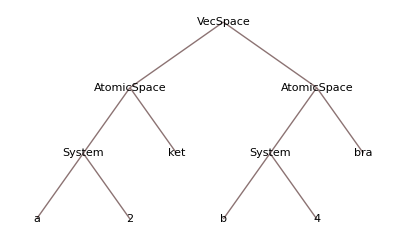

```mathematica
sp1=VecSpace[asp1,asp2];
sp2=VecSpace[asp3];
sp1//TreeForm
```

```mathematica
AtomNames[x_VecSpace]:=Level[x,{3}][[;;;;2]];
AtomicQ[x_VecSpace]:=Length[x]==1;
AtomDimensions[x_VecSpace]:=Level[x,{3}][[2;;;;2]];
Dimension[x_VecSpace]:=Times@@AtomDimensions[x];
```

```mathematica
AtomNames[sp1]
```

{a,b}

```mathematica
AtomNames[sp1]
```

{a,b}

to get the leaves, use Level {-1}

```mathematica
Map[List@@#&,sp1,{0,1}]
```

{{System[a,2],ket},{System[b,4],bra}}

```mathematica
Level[sp1,{-1}]
```

{a,2,ket,b,4,bra}

#### IndexDict

Index dictionary: list of vector spaces. Shouldn’t contain AtomicSpaces with the same name and type.

```mathematica
td1=IndexDict[sp1,sp2]
```

IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

```mathematica
td2=IndexDict[VecSpace[AtomicSpace[b,"ket"]],VecSpace[AtomicSpace[d,"bra"]]]
```

IndexDict[VecSpace[AtomicSpace[System[b,4],ket]],VecSpace[AtomicSpace[System[d,7],bra]]]

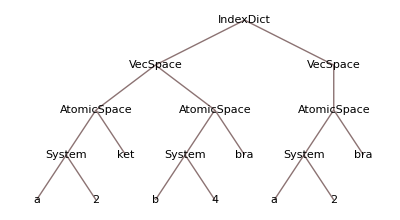

```mathematica
td1//TreeForm
```

```mathematica
Atoms[x_IndexDict]:=Level[x,{2}];
Atomize[x_IndexDict]:=IndexDict@@(VecSpace[#]&/@Atoms[x]);
AtomicQ[x_IndexDict]:=And@@(AtomicQ/@x);
AtomNames[x_IndexDict]:=Level[x,{4}][[;;;;2]]
```

```mathematica
(VecSpace[#]&/@Atoms[td1])
```

{VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]}

```mathematica
AtomicQ[Atomize[td1]]
```

True

```mathematica
(AtomicQ/@td1)
```

IndexDict[False,True]

```mathematica
Atomize[td1]
```

IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

```mathematica
Kets[x_IndexDict]:=Select[Atoms[x],#[[2]]=="ket"&]
Bras[x_IndexDict]:=Select[Atoms[x],#[[2]]=="bra"&]
```

```mathematica
Bras[td1]
```

{AtomicSpace[System[b,4],bra],AtomicSpace[System[a,2],bra]}

```mathematica
Name/@Bras[td1]
```

{b,a}

```mathematica
td1
```

IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

```mathematica
SystemMapping[x_IndexDict]:=MapDict@@(Map[Name,{Kets[x],Bras[x]},{2}]);
ValidMappingQ[x_IndexDict]:=ValidMappingQ[SystemMapping[x]];
ComposableQ[L_IndexDict,R_IndexDict]:=ComposableQ[SystemMapping@L,SystemMapping@R]
```

```mathematica
SystemMapping[td1]
```

MapDict[{a},{b,a}]

```mathematica
td2//SystemMapping
```

MapDict[{b},{d}]

these are for atomic IndexDicts only

```mathematica
NameSort[x_IndexDict/;AtomicQ[x]]:=IndexDict@@(VecSpace[#]&/@SortBy[Level[x,{2}],{Name,Type[#]=="bra"&}])
TypeSort[x_IndexDict/;AtomicQ[x]]:=IndexDict@@(VecSpace[#]&/@SortBy[Level[x,{2}],{Type[#]=="bra"&,Name}])
```

these as well. all of these are really bad in the sense that they would produce syntactically-valid output from non-atomic IndexDicts, but the outputs don’t mean anything useful in terms of the original object.

```mathematica
KetIndices[x_IndexDict]:=Flatten[Position[Atoms[x],z_/;Type[z]=="ket"]];
BraIndices[x_IndexDict]:=Flatten[Position[Atoms[x],z_/;Type[z]=="bra"]]
```

```mathematica
CompositionIndices[L_IndexDict,R_IndexDict]:=Flatten[{Position[Atoms@L,z_/;Type[z]=="bra"&&Name[z]==#],Position[Atoms@R,z_/;Type[z]=="ket"&&Name[z]==#]}]&/@(ContractableSystems@@(SystemMapping[#]&/@{L,R}));
```

```mathematica
ComposeMaps[L_IndexDict/;AtomicQ[L],R_IndexDict/;AtomicQ[R]]:=Module[{ci=CompositionIndices[L,R]},
If[ci=={},IndexDict@@(Join[L,R]),IndexDict@@(Join@@MapThread[Delete,{{L,R},Transpose[{#}]&/@Transpose[CompositionIndices[L,R]]}])]]
```

```mathematica
ComposeMaps[Atomize[td1],td2]//SystemMapping
```

MapDict[{a},{a,d}]

```mathematica
ComposeMaps[td2,Atomize[td1]]//SystemMapping
```

MapDict[{b,a},{d,b,a}]

```mathematica
AtomicQ[td2]
```

True

#### MultiMap

it seems that we have to separately deal with the exceptional case of maps from C to C (i.e. numbers). This case is exceptional because the array in the second slot of MultiMap is now just a number; it has no dimensions, and so it doesn’t work with ArrayReshape.

```mathematica
AtomicQ[t_MultiMap]:=And[AtomicQ[t[[1]]],List@@Dimension/@Atoms[t[[1]]]==Dimensions[t[[2]]]];Atomize[t_MultiMap]:=
If[AtomicQ[t],t,
Module[{atomdict=Atomize[t[[1]]]},
MultiMap@@{atomdict,ArrayReshape[t[[2]],List@@Dimension/@atomdict]}]];
```

```mathematica
ComposableQ[L_MultiMap,R_MultiMap]:=ComposableQ[L[[1]],R[[1]]];
```

```mathematica
ComposeAtomicTensors[L_MultiMap,R_MultiMap]:=If[ComposableQ[L[[1]],R[[1]]],MultiMap@@{ComposeMaps[L[[1]],R[[1]]],Activate[TensorContract[Inactive[TensorProduct][L[[2]],R[[2]]],(#+{0,Length[L[[1]]]})&/@CompositionIndices[L[[1]],R[[1]]]]]}]
```

```mathematica
ComposeMaps[L_MultiMap,R_MultiMap]:=ComposeAtomicTensors[Atomize[L],Atomize[R]];
```

```mathematica
SystemMapping[t_MultiMap]:=SystemMapping[t[[1]]]
```

```mathematica
t1=MultiMap[td1,RandomReal[{0,1},{8,2}]];
t2=MultiMap[td2,RandomReal[{0,1},{4,7}]];
testket=MultiMap[IndexDict[VecSpace[AtomicSpace[System["a",2],"ket"]]],RandomReal[{0,1},{2}]];
testbra=MultiMap[IndexDict[VecSpace[AtomicSpace[System["a",2],"bra"]]],RandomReal[{0,1},{2}]];
trivial=ComposeAtomicTensors[testbra,testket];
```

```mathematica
SystemMapping[t2]
```

MapDict[{b},{d}]

```mathematica
Atomize[testbra]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],bra]]],{0.450867,0.102993}]

```mathematica
genPerm[list1_,list2_]:=Flatten[Position[list1,#]&/@list2];
SortMap[x_IndexDict/;AtomicQ[x],f_]:=genPerm[List@@(f[x]),List@@x]
```

```mathematica
SortMap[Atomize[td1],TypeSort]
```

{1,3,2}

Canonical is kets then bras, i.e. Type sorted.

```mathematica
Canonicalize[t_MultiMap]:=
If[Length[t[[1]]]==0,t,MultiMap@@{TypeSort[#[[1]]],Transpose[#[[2]],SortMap[#[[1]],TypeSort]]}&[Atomize[t]]];
Matrixize[t_MultiMap]:=
Module[{ct,keti,brai},
ct=Canonicalize[t];
keti=KetIndices[ct[[1]]];
brai=BraIndices[ct[[1]]];
Which[
keti=={}&&brai=={},
MultiMap[IndexDict[],ct[[2]]],
keti=={}||brai=={},
MultiMap[IndexDict[VecSpace@@Atoms[ct[[1]]]],Flatten[ct[[2]]]],
True,
MultiMap@@({IndexDict@@(VecSpace[#]&/@SplitBy[List@@Atoms[ct[[1]]],Type]),Flatten[ct[[2]],{keti,brai}]})]]
```

```mathematica
Canonicalize[trivial]
```

MultiMap[IndexDict[],0.411267]

```mathematica
ComposeMaps[t2,t1]//SystemMapping
```

MapDict[{b,a},{d,b,a}]

```mathematica
Matrixize[ComposeMaps[t2,t1]][[2]]//SingularValueList
```

{5.69956,2.05113,1.84173,1.082,0.662792,0.596866,0.389383,0.214797}

```mathematica
basisElement[sys_,num_,type_]:=MultiMap@@{IndexDict[VecSpace[AtomicSpace[sys,type]]],SparseArray[{num+1->1},{Dimension[sys]}]};basisKet[sys_,num_]:=
basisElement[sys,num,"ket"];
basisBra[sys_,num_]:=basisElement[sys,num,"bra"];
```

```mathematica
basisElement[a,1,"ket"]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]]],SparseArray[<1>, {2}]]

```mathematica
testket
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]]],{0.549284,0.259767}]

```mathematica
ComposeMaps[basisBra[a,0],testket]
```

MultiMap[IndexDict[],0.549284]

```mathematica
SystemMapping[t2]
SystemMapping[t1]
```

MapDict[{b},{d}]

MapDict[{a},{b,a}]

```mathematica
Canonicalize[t1]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[a,2],bra]],VecSpace[AtomicSpace[System[b,4],bra]]],{{{0.398351,0.330669,0.874514,0.789326},{0.969347,0.99864,0.00259545,0.998205}},{{0.432152,0.467101,0.924672,0.72963},{0.239969,0.420696,0.305539,0.477364}}}]

```mathematica
KetIndices[MultiMap[IndexDict[],0.29597124389250995]]
```

KetIndices[MultiMap[IndexDict[],0.295971]]

```mathematica
testket[[2]]//Norm
```

0.607611

```mathematica
{testket[[2]]}//SingularValueList
```

{0.607611}

```mathematica
makeCanonical[t1]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[False].

Transpose::list: List expected at position 2 in Transpose[MultiMap[IndexDict[VecSpace[AtomicSpace[System["a", 2], "ket"]], VecSpace[AtomicSpace[System["b", 4], "bra"]], VecSpace[AtomicSpace[System["a", 2], "bra"]]], {{0.15965, 0.348782}, {0.0971431, 0.109028}, « 5 », {0.652819, 0.269328}}], Flatten[False]].

MultiMap[TypeSort[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]==IndexDict[]],Transpose[MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]],{{0.15965,0.348782},{0.0971431,0.109028},{0.102568,0.648692},{0.802404,0.187038},{0.395949,0.84404},{0.177322,0.528443},{0.431452,0.622575},{0.652819,0.269328}}],Flatten[False]]]

```mathematica
VecSpace@@Atoms[td1]
```

VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra],AtomicSpace[System[a,2],bra]]

```mathematica
List@@Dimension/@IndexDict[]
```

{}

```mathematica
testket
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]]],{0.180653,0.905646}]

```mathematica
Atomize[IndexDict[]]
```

IndexDict[]

```mathematica
makeCanonical[MultiMap[IndexDict[],0.3479437041322474]]
```

Transpose::list: List expected at position 2 in Transpose[0.347944, IndexDict[]].

MultiMap[IndexDict[],Transpose[0.347944,IndexDict[]]]

```mathematica
TypeSort[IndexDict[]]
```

IndexDict[]

```mathematica
SystemMapping[MultiMap[IndexDict[],0.3479437041322474]]
```

MapDict[{},{}]

```mathematica
td1
```

IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

```mathematica
Dimension[VecSpace[]]
```

Part::take: Cannot take positions 2 through -1 in {}.

{}

```mathematica
AtomicQ[t1]
```

False

```mathematica
AtomicQ[Atomize[t1]]
```

True

```mathematica
Dimension/@Atoms[td1]
```

{2,4,2}

```mathematica
td1
```

IndexDict[VecSpace[AtomicSpace[System[a,2],ket],AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

MultiMap[IndexDict[VecSpace[AtomicSpace[System[b,4],ket]],VecSpace[AtomicSpace[System[d,7],bra]]],{{0.53438,0.287995,0.64531,0.53736,0.481176,0.39282,0.541349},{0.0494161,0.0824318,0.887234,0.164378,0.473109,0.277107,0.674586},{0.134865,0.528914,0.984423,0.187782,0.13805,0.801253,0.595785},{0.705281,0.138256,0.354786,0.439544,0.989133,0.685008,0.813878}}]

```mathematica
AtomicQ[td2]
```

True

```mathematica
AtomicQ[t2]
```

True

```mathematica
ComposeAtomicTensors[Atomize[t1],t2]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[a,2],bra]],VecSpace[AtomicSpace[System[d,7],bra]]],{{{0.669867,0.219173,0.574864,0.47371,0.930623,0.721469,0.866125},{0.41117,0.478397,1.02675,0.409367,0.493965,0.81511,0.801069}},{{0.738959,0.447106,1.06918,0.609877,0.979701,0.997563,1.12233},{0.751067,0.653165,1.72195,0.775708,1.00849,1.16132,1.40352}}}]

```mathematica
Dimension/@ComposeAtomicTensors[t2,Atomize[t1]][[1]]
```

IndexDict[4,7,2,4,2]

```mathematica
Dimensions[ComposeAtomicTensors[t2,Atomize[t1]][[2]]]
```

{4,7,2,4,2}

```mathematica
makeAtomic[t1][[1]]//AtomicQ
```

True

```mathematica
ComposeAtomicTensors[t2,Atomize[t1]][[1]]
```

IndexDict[VecSpace[AtomicSpace[System[b,4],ket]],VecSpace[AtomicSpace[System[d,7],bra]],VecSpace[AtomicSpace[System[a,2],ket]],VecSpace[AtomicSpace[System[b,4],bra]],VecSpace[AtomicSpace[System[a,2],bra]]]

```mathematica
List@@Dimension/@Atomize[td1]
```

{2,4,2}